## lapse

```mathematica
f[r_,ζ_]=(1- 2/r+ζ^2/r^2(1-2/r)^2);
```

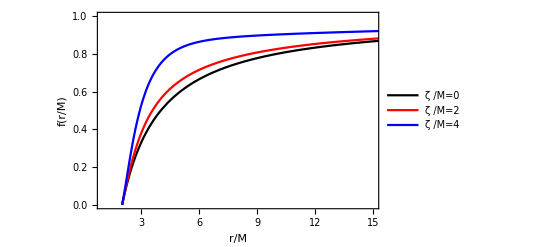

```mathematica
Plot[{f[r,0],f[r,2],f[r,4]},{r,1.7,18},PlotStyle->{Black,Red,Blue,Green},PlotRange->{{1.,15},{0,1}},Frame->True,FrameLabel->{"r/M","f(r/M)"},PlotLegends->Placed[{"ζ /M=0","ζ /M=2","ζ /M=4"},{Scaled[{0.70,0.5}],{0,0.5}}],LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15}]
```

## redshift parameter z

```mathematica
g00[r_,ζ_]=-(1- 2/r+ζ^2/r^2(1-2/r)^2);
z[r_,ζ_]= √((-r^2* D[g00[r,ζ],r])/(g00[r,ζ]*(2*r *g00[r,ζ]-r^2* D[g00[r,ζ],r])));
```

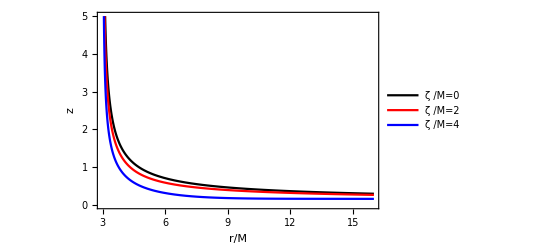

```mathematica
Plot[{z[r,0],z[r,2],z[r,4]},{r,3,16},PlotStyle->{Black,Red,Blue,Green},PlotRange->{{3,15.97},{0.,5}},Frame->True,FrameLabel->{"r/M","z"},PlotLegends->Placed[{"ζ /M=0","ζ /M=2","ζ /M=4"},{Scaled[{0.70,0.78}],{0,0.5}}],LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15}]
```

### density plot 1

```mathematica
z[r,ζ]
```

√(-(r^2 (-2/r^2-(4 (1-2/r) ζ^2)/r^4+(2 (1-2/r)^2 ζ^2)/r^3))/((-1+2/r-((1-2/r)^2 ζ^2)/r^2) (-r^2 (-2/r^2-(4 (1-2/r) ζ^2)/r^4+(2 (1-2/r)^2 ζ^2)/r^3)+2 r (-1+2/r-((1-2/r)^2 ζ^2)/r^2))))

```mathematica
z[75.2,6]
```

0.0883477

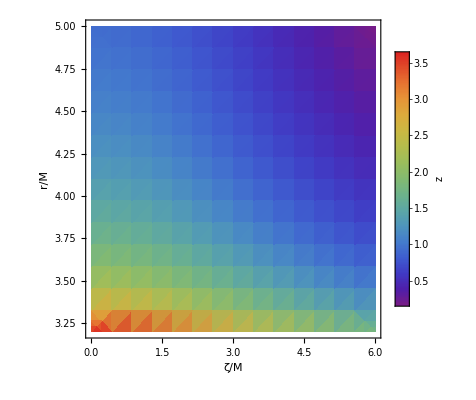

```mathematica
DensityPlot[z[r,ζ],{ζ,0,6},{r,3.2,5},ColorFunction->"Rainbow",PlotLegends->BarLegend[ Automatic,LegendLabel->"z",LegendMarkerSize->280],FrameLabel->{"ζ/M","r/M"},Frame->True,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15}]
```

## Veff

```mathematica
Veff[r_,ζ_,Ene_,L_]=(Ene^2 r^2 + L^2 g00[r,ζ])/(g00[r,ζ] r^2)+1;
```

```mathematica
ve[r_,ζ_]=√(f[r,ζ] (6/r^2))
```

√6 √((1-2/r+((1-2/r)^2 ζ^2)/r^2)/r^2)

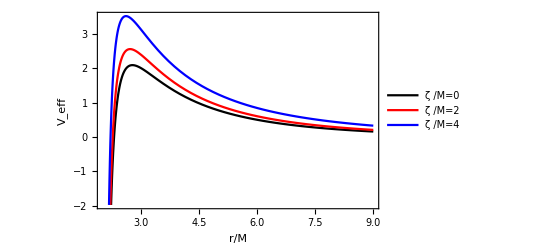

```mathematica
Plot[{Veff[r,0,1,6],Veff[r,2,1,6],Veff[r,4,1,6]},{r,2,9},PlotStyle->{Black,Red,Blue},PlotLegends->Placed[{"ζ /M=0","ζ /M=2","ζ /M=4"},{Scaled[{0.70,0.25}],{0,0.5}}],LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},Frame->True,FrameLabel->{"r/M","V_eff"},PlotRange->{{},{}}]
```

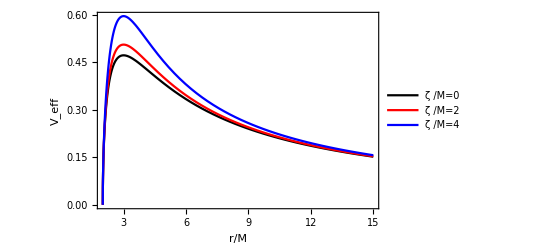

```mathematica
Plot[{ve[r,0],ve[r,2],ve[r,4]},{r,2,15},PlotStyle->{Black,Red,Blue},PlotLegends->Placed[{"ζ /M=0","ζ /M=2","ζ /M=4"},{Scaled[{0.70,0.65}],{0,0.5}}],LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},Frame->True,FrameLabel->{"r/M","V_eff","L=6"}]
```

## Kretschman scalar

```mathematica
K[r_,ζ_]=1/r^12 8 (936 ζ^4 M^4-8 M^3 (15 ζ^2 r^3+146 ζ^4 r)+M^2 (6 r^6+80 ζ^2 r^4+524 ζ^4 r^2)-4 M (3 ζ^2 r^5+25 ζ^4 r^3)+7 ζ^4 r^4)/.M->1
```

1/r^12 8 (6 r^6+80 r^4 ζ^2+936 ζ^4+524 r^2 ζ^4+7 r^4 ζ^4-8 (15 r^3 ζ^2+146 r ζ^4)-4 (3 r^5 ζ^2+25 r^3 ζ^4))

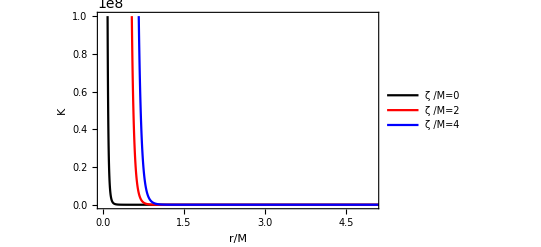

```mathematica
Plot[{K[r,0],K[r,2],K[r,4]},{r,0,9},PlotStyle->{Black,Red,Blue},PlotLegends->Placed[{"ζ /M=0","ζ /M=2","ζ /M=4"},{Scaled[{0.60,0.45}],{0,0.5}}],LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},Frame->True,FrameLabel->{"r/M","K"},PlotRange->{{0,5},{-100000,100000000.5}}]
```

```mathematica
K[r,1]
```

(8 (936+524 r^2+87 r^4+6 r^6-8 (146 r+15 r^3)-4 (25 r^3+3 r^5)))/r^12